# Static Analytic Solutions Calculation

## Clear All Variables

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
timeStart=Now;
```

```mathematica
TimeEstIridis5[A_]=0.318355815129576+6.347218507768962*^-11 A;
```

## Inputs

```mathematica
l = 0;
rp =8;
```

## Calculation

```mathematica
ρp = rp-1;

Ε=(rp-2)/(rp Sqrt[1-3/rp])//N

jumpψ = 0;
jumpψr =-(2 Conjugate[SphericalHarmonicY[l,0,Pi/2,0]])/(Ε rp);

ψin[r_] := A r LegendreP[l,r-1];
ψout[r_] := FullSimplify[B r LegendreQ[l,0,3,r-1]];

ψinp = ψin[rp];
ψoutp = ψout[rp];

Dψinp = D[ψin[r],r] /. r-> rp;
Dψoutp = D[ψout[r],r] /. r-> rp;

sol= Solve[{ψoutp - ψinp == jumpψ, Dψoutp - Dψinp == jumpψr}/.{A->A1,B->B1},{A1,B1}][[1]];
{A,B}={sol[[1,2]],sol[[2,2]]};
```

0.948683

```mathematica
0.9561828874675149
```

0.956183

Check that solutions are correct (results should be 0)

```mathematica
ψout[rp]-ψin[rp]-jumpψ //FullSimplify
ψout'[rp]-ψin'[rp]-jumpψr//FullSimplify
```

0.

2.77556×10^-17

```mathematica
-7.0924531027638515*^-6
```

-7.09245×10^-6

```mathematica
4π (1-2/rp)^2/(Ε rp)Conjugate[SphericalHarmonicY[l,0,Pi/2,0]]//N
```

0.262734

```mathematica
-0.26527660175826173
```

-0.265277

```mathematica
-0.2652766017582617/0.2485
```

-1.06751

## Output

```mathematica
2 Pi ψout[rp]//N
NumberForm[2 Pi ψout[rp],16]
```

3.22491

3.224910978414768

```mathematica
2 Pi jumpψr//N
```

-0.467083

```mathematica
0.41449469024728386/0.388
```

1.06829

```mathematica
[]
Needs["MaTeX`"]
```

PacletObject[…]

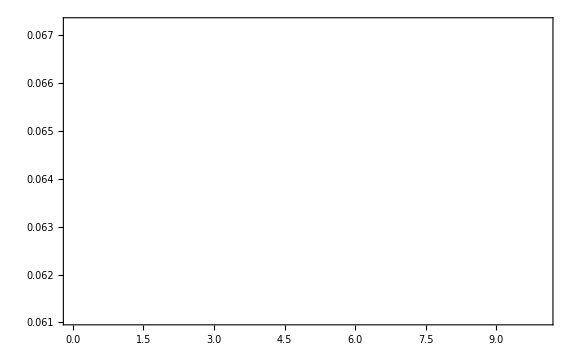

```mathematica
Show[Plot[ψin[r]/r,{r,0,rp} ,PlotRange->{{0,10},Automatic(*{0.0035,0.0135}*)}],Plot[ψout[r]/r,{r,rp,10},PlotStyle->ColorData[97,"ColorList"][[2]] ],ImageSize->Large,Frame->True,GridLines->{{rp},{rp}},FrameLabel->{{MaTeX["\\psi_{00}",FontSize->20],None},{MaTeX["r/M",FontSize->20],None}},FrameTicksStyle->Directive[FontSize->18],Epilog->{Text[MaTeX["\\psi^-",FontSize->30],Scaled@{0.25,0.9}],Text[MaTeX["\\psi^+",FontSize->30],Scaled@{0.75,0.9}]}]
```